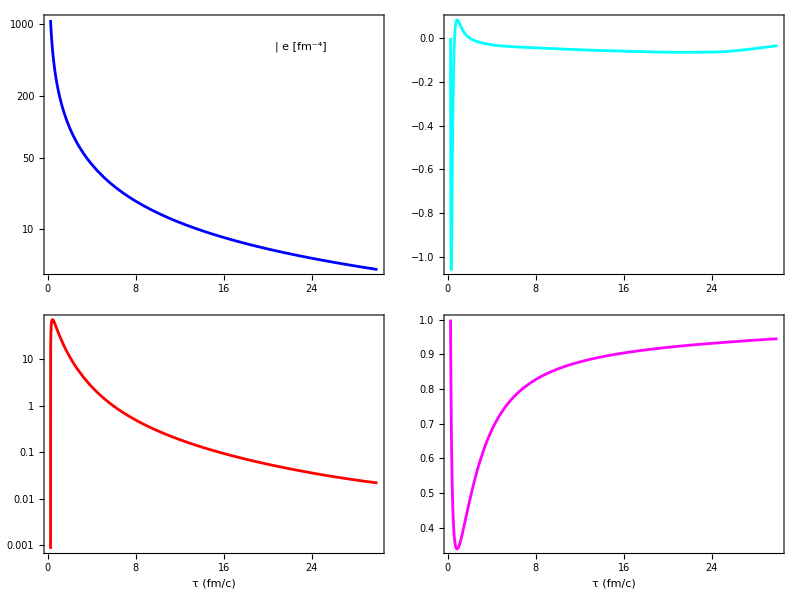

Fig1.pdf

```mathematica
ClearAll["Global`*"]

wd=SetDirectory@NotebookDirectory[];

(*styles={Directive[RGBColor[0,0.4,0.5],AbsoluteThickness[3],AbsoluteDashing[{10,5}]],Directive[RGBColor[0.8,0.2,0.2],AbsoluteThickness[3],AbsoluteDashing[{10,5}]],
Directive[RGBColor[0.5,0.0,0.9],AbsoluteThickness[3],AbsoluteDashing[{10,5}]],Directive[RGBColor[0.0,0.6,0.0],AbsoluteThickness[3],AbsoluteDashing[{10,5}]]};*)

styles={Directive[RGBColor[0,0.0,1.0],AbsoluteThickness[2]],Directive[RGBColor[1,0,0],AbsoluteThickness[2]],
Directive[RGBColor[0,1,1],AbsoluteThickness[2]],Directive[RGBColor[1,0,1],AbsoluteThickness[2]]};

EnergyDensityDataRaw=Import[wd<>"/eplot.dat"];
piDataRaw=Import[wd<>"/piplot.dat"];
PiDataRaw=Import[wd<>"/bulkplot.dat"];
plptDataRaw=Import[wd<>"/plptplot.dat"];

EnergyDensityData= Take[EnergyDensityDataRaw,{2,Length[EnergyDensityDataRaw]}];
piData= Take[piDataRaw,{2,Length[piDataRaw]}];
PiData= Take[PiDataRaw,{2,Length[PiDataRaw]}];
plptData= Take[plptDataRaw,{2,Length[plptDataRaw]}];

t0 = EnergyDensityData[[1,1]];
tf = EnergyDensityData[[Length[EnergyDensityData],1]];

energydensity = Interpolation[EnergyDensityData[[All,{1,2}]]];
pi = Interpolation[piData[[All,{1,2}]]];
bulk = Interpolation[PiData[[All,{1,2}]]];
plpt = Interpolation[plptData[[All,{1,2}]]];

legend1=Panel[Grid[{{Graphics[{styles[[1]],Line[{{0,0},{1,0}}]},ImageSize->45,AspectRatio->0.2],Style["e [fm^-4]",FontSize->18,FontFamily->"Times"]}}],Background->White];
legend2=Panel[Grid[{{Graphics[{styles[[2]],Line[{{0,0},{1,0}}]},ImageSize->44,AspectRatio->0.2],Style["π [fm^-4]",FontSize->18,FontFamily->"Times"]}}],Background->White];
legend3=Panel[Grid[{{Graphics[{styles[[3]],Line[{{0,0},{1,0}}]},ImageSize->45,AspectRatio->0.2],Style["Π [fm^-4]",FontSize->18,FontFamily->"Times"]}}],Background->White];
legend4=Panel[Grid[{{Graphics[{styles[[4]],Line[{{0,0},{1,0}}]},ImageSize->44,AspectRatio->0.2],Style["P_L/P_⊥",FontSize->18,FontFamily->"Times"]}}],Background->White];

picture=Grid[{{LogPlot[{energydensity[t]},{t,t0,tf},PlotRange->All,PlotStyle->styles[[1]],ImageSize->320,Frame->True,Axes->False,BaseStyle->{FontSize->16},AspectRatio->0.75,Epilog->Inset[legend1,{23,6.4}]],
Plot[{bulk[t]},{t,t0,tf},PlotRange->All,PlotStyle->styles[[3]],ImageSize->321,Frame->True,Axes->False,BaseStyle->{FontSize->16},AspectRatio->0.75]},
{LogPlot[{pi[t]},{t,t0,tf},PlotRange->All,PlotStyle->styles[[2]],ImageSize->320,Frame->True,Axes->False,FrameLabel->{"τ (fm/c)",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{plpt[t]},{t,t0,tf},PlotRange->All,PlotStyle->styles[[4]],ImageSize->320,Frame->True,Axes->False,FrameLabel->{"τ (fm/c)",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]

Export["Fig1.pdf",picture]
```

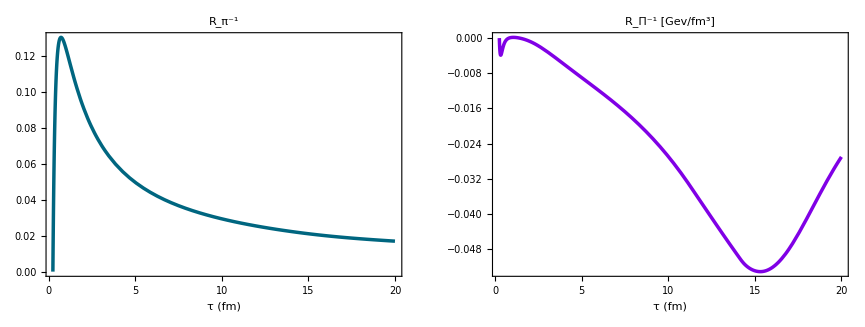

```mathematica
RpiInverseDataRaw=Import[wd<>"/RpiInvplot.dat"];
RbulkInverseDataRaw=Import[wd<>"/RbulkInvplot.dat"];

RpiInverseData= Take[RpiInverseDataRaw,{2,Length[RpiInverseDataRaw]}];
RbulkInverseData= Take[RbulkInverseDataRaw,{2,Length[RbulkInverseDataRaw]}];


t0 = EnergyDensityData[[1,1]];
tf = EnergyDensityData[[Length[EnergyDensityData],1]];

RpiInverse = Interpolation[RpiInverseData[[All,{1,2}]]];
RbulkInverse = Interpolation[RbulkInverseData[[All,{1,2}]]];


Print[GraphicsGrid[{{Plot[{RpiInverse[t]},{t,t0,tf},PlotRange->All,PlotStyle->styles[[1]],ImageSize->400,Frame->True,Axes->False,PlotLabel->Style["R_π^-1",FontSize->24],FrameLabel->{"τ (fm)",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{RbulkInverse[t]},{t,t0,tf},PlotRange->All,PlotStyle->styles[[3]],ImageSize->400,Frame->True,Axes->False,PlotLabel->Style["R_Π^-1 [Gev/fm^3]",FontSize->24],FrameLabel->{"τ (fm)",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]]
```

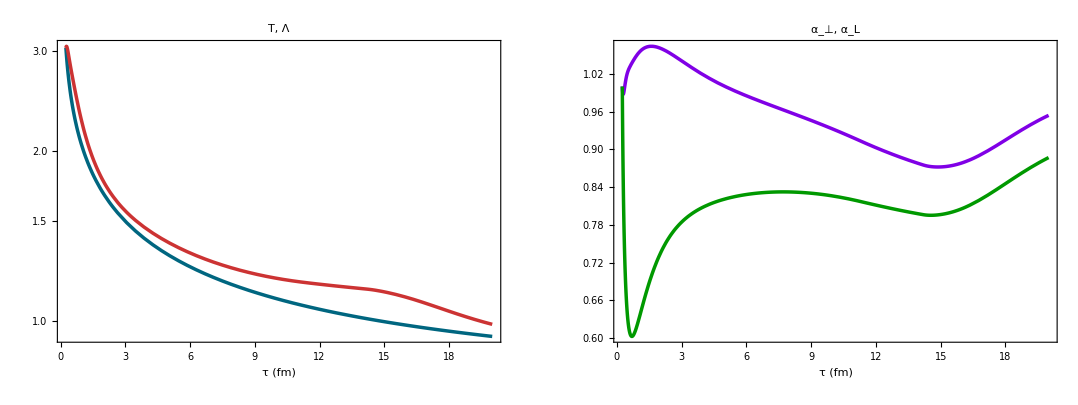

```mathematica
TDataRaw=Import[wd<>"/Tplot.dat"];
lambdaDataRaw=Import[wd<>"/lambdaplot.dat"];
axDataRaw=Import[wd<>"/axplot.dat"];
azDataRaw=Import[wd<>"/azplot.dat"];

TData= Take[TDataRaw,{2,Length[TDataRaw]}];
lambdaData= Take[lambdaDataRaw,{2,Length[lambdaDataRaw]}];
axData= Take[axDataRaw,{2,Length[axDataRaw]}];
azData= Take[azDataRaw,{2,Length[azDataRaw]}];


T = Interpolation[TData[[All,{1,2}]]];
lambda = Interpolation[lambdaData[[All,{1,2}]]];
ax = Interpolation[axData[[All,{1,2}]]];
az = Interpolation[azData[[All,{1,2}]]];



Print[GraphicsGrid[{{LogPlot[{T[t],lambda[t]},{t,t0,tf},PlotRange->All,PlotStyle->styles[[1;;2]],ImageSize->500,Frame->True,Axes->False,PlotLabel->Style["T, Λ",FontSize->24],FrameLabel->{"τ (fm)",""},BaseStyle->{FontSize->16},AspectRatio->0.75],
Plot[{ax[t],az[t]},{t,t0,tf},PlotRange->All,PlotStyle->styles[[3;;4]],ImageSize->500,Frame->True,Axes->False,PlotLabel->Style["α_⊥, α_L",FontSize->24],FrameLabel->{"τ (fm)",""},BaseStyle->{FontSize->16},AspectRatio->0.75]}}]]
```